```mathematica
kRed=1;
kGreen=2;
kOrange=3;
kBlue=4;
kMagenta=5;
kCyan=6;
kYellow=7;
kBrown=8;
kSky=9;
```

```mathematica
ClearAll[ParseListPos,PlotPartridgeTiling,RepeatedAlphabet]
ParseListPos[n_][str_]:=ParseListPos[n,str];
ParseListPos[n_,str_]:=ToExpression@StringReplace[StringSplit[str,"\n"],
{("["|"(")->"{",("]"|")")->"}"}]//Map[Join[Transpose[{Table[Splice@Table[k,k],{k,1,n}]}],#,2]&];
Options[PlotPartridgeTiling]={"ColumnLetters"->{},"RowLetters"->{},"ColorMap"->Automatic};
PlotPartridgeTiling[n_Integer,pos_List,opts:OptionsPattern[Graphics|PlotPartridgeTiling]]:=
Module[{l=n(n+1)/2,cmap,charsrule,colchargr,rowchargr,colorrule},
colorrule=FilterRules[{opts},"ColorMap"];
cmap=Association@If[colorrule=={},
Map[Reverse]@{Red->1,Green->2,Orange->3,Blue->4,Magenta->5,Lighter[RGBColor[0., 0.5, 1.]]->6,Yellow->7,Brown->8,LightBlue->9},
"ColorMap"/.colorrule
];
charsrule=FilterRules[{opts},{"ColumnLetters","RowLetters"}];
colchargr[x_,c_]:={FaceForm[None],EdgeForm[None],Rectangle[{c-1,1/2},{c,3/2}],Text[Style[x,11,Bold],{-1/2+c,1}]};
rowchargr[x_,r_]:={FaceForm[None],EdgeForm[None],Rectangle[{-1/2,1-r},{-3/2,-r}],Text[Style[x,11,Bold],{-1,1/2-r}]};
Graphics[{
{EdgeForm[{Black,Thin}],FaceForm[None],Rectangle[{l, 0}, {0, -l}]},
MapApply[{EdgeForm[{Black,Thin}],FaceForm[Lookup[cmap,#1,None]],Rectangle[{#3,-#2},{#3+#1,-#2-#1}]}&,pos],
MapApply[colchargr,"ColumnLetters"/.charsrule/.Options[PlotPartridgeTiling]],
MapApply[rowchargr,"RowLetters"/.charsrule/.Options[PlotPartridgeTiling]]
},Sequence@@FilterRules[{opts},Keys@Options[Graphics]]]
];
RepeatedAlphabet[n_Integer,i_Integer, highlighted:_List:{}]:=Module[{l=n(n+1)/2, chars},
chars=PadRight[{},l,RotateLeft[CharacterRange["A","Z"],Mod[(i-1)*l,26]]];
MapIndexed[If[MemberQ[highlighted, First[#2]],Style[#1, Red], #1]->First[#2]&,chars]
]
```

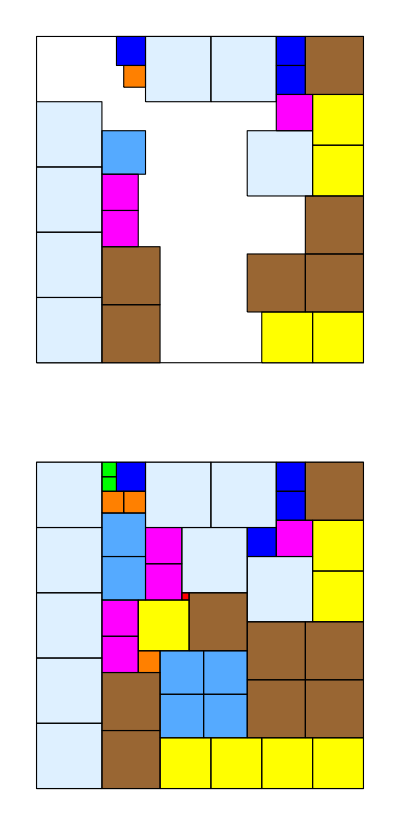

```mathematica
lst1= {
{kSky,9,0},{kSky,18,0},{kSky,27,0},{kSky,36,0},{kBrown,37,9},{kBrown,29,9},{kMagenta,24,9},{kMagenta,19,9},{kCyan,13,9},{kYellow,38,31},{kYellow,38,38},{kBrown,30,37},{kBrown,30,29},{kBrown,22,37},{kSky,13,29},{kYellow,15,38},{kYellow,8,38},{kBrown,0,37},{kBlue,0,33},{kBlue,4,33},{kMagenta,8,33},{kSky,0,24},{kSky,0,15},{kBlue,0,11},{kOrange,4,12}
};
sols1="[(18, 20), (0, 9), (2, 9), (4, 12), (4, 9), (26, 14), (0, 33), (4, 33), (0, 11), (9, 29), (24, 9), (19, 9), (8, 33), (9, 15), (14, 15), (13, 9), (7, 9), (26, 17), (26, 23), (32, 17), (32, 23), (38, 31), (38, 38), (15, 38), (8, 38), (19, 14), (38, 17), (38, 24), (37, 9), (29, 9), (30, 37), (30, 29), (22, 37), (0, 37), (18, 21), (22, 29), (9, 0), (18, 0), (27, 0), (36, 0), (13, 29), (0, 24), (0, 15), (0, 0), (9, 20)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst1]},Map[PlotPartridgeTiling[9,#]&,sols1]}]
```

Length  31

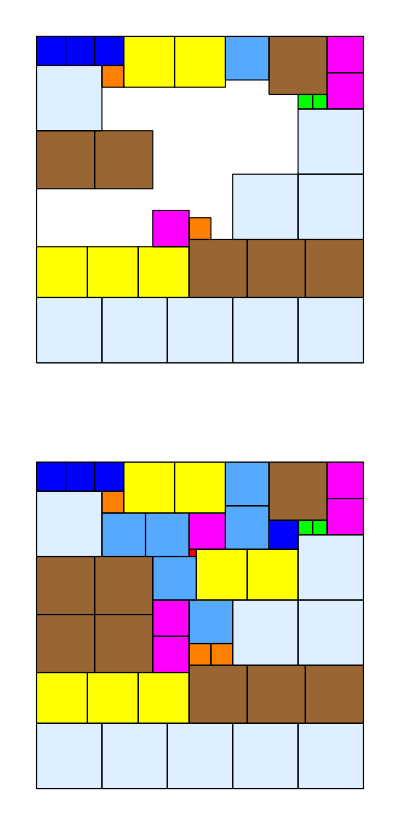

```mathematica
lst2= {
{kSky,36,0},{kSky,36,9},{kSky,36,18},{kSky,36,27},{kSky,36,36},
{kYellow,29,0},{kYellow,29,7},{kYellow,29,14},
{kBrown,28,21},{kBrown,28,29},{kBrown,28,37},
{kMagenta,24,16},{kOrange,25,21},
{kSky,19,36},{kSky,19,27},{kSky,10,36},
{kMagenta,0,40},{kMagenta,5,40},{kBrown,0,32},{kCyan,0,26},
{kYellow,0,19},{kYellow,0,12},{kBlue,0,0},{kBlue,0,4},{kBlue,0,8},
{kSky,4,0},{kOrange,4,9},
{kBrown,13,0},{kBrown,13,8},
{kGreen,8,36},{kGreen,8,38}
}//Echo[#,Length,Length]&;
sols2="[(12, 21), (8, 36), (8, 38), (25, 21), (4, 9), (25, 24), (0, 0), (0, 4), (0, 8), (8, 32), (24, 16), (0, 40), (5, 40), (7, 21), (19, 16), (0, 26), (6, 26), (7, 9), (7, 15), (13, 16), (19, 21), (29, 0), (29, 7), (29, 14), (0, 19), (0, 12), (12, 22), (12, 29), (28, 21), (28, 29), (28, 37), (0, 32), (13, 0), (13, 8), (21, 0), (21, 8), (36, 0), (36, 9), (36, 18), (36, 27), (36, 36), (19, 36), (19, 27), (10, 36), (4, 0)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst2]},Map[PlotPartridgeTiling[9,#]&,sols2]}]
```

Length  31

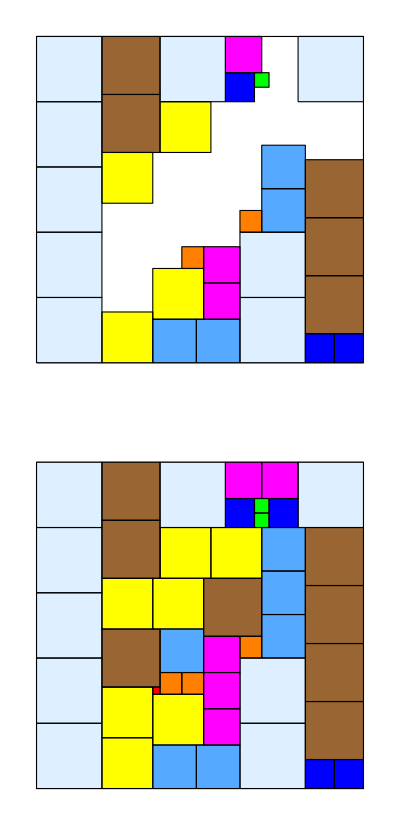

```mathematica
lst3= {
{kSky,0,0},{kSky,9,0},{kSky,18,0},{kSky,27,0},{kSky,36,0},
{kBrown,0,9},{kBrown,8,9},{kYellow,16,9},{kYellow,38,9},
{kSky,0,17},{kYellow,9,17},{kMagenta,0,26},{kBlue,5,26},{kGreen,5,30},{kSky,0,36},
{kCyan,39,16},{kCyan,39,22},{kYellow,32,16},{kOrange,29,20},
{kMagenta,34,23},{kMagenta,29,23},{kSky,36,28},{kSky,27,28},
{kOrange,24,28},{kCyan,21,31},{kCyan,15,31},{kBlue,41,37},{kBlue,41,41},{kBrown,33,37},{kBrown,25,37},{kBrown,17,37}
}//Echo[#,Length,Length]&;
sols3="[(31, 16), (5, 30), (7, 30), (29, 20), (24, 28), (29, 17), (5, 26), (41, 37), (41, 41), (5, 32), (0, 26), (34, 23), (29, 23), (0, 31), (24, 23), (39, 16), (39, 22), (21, 31), (15, 31), (9, 31), (23, 17), (16, 9), (38, 9), (9, 17), (32, 16), (9, 24), (16, 16), (31, 9), (0, 9), (8, 9), (33, 37), (25, 37), (17, 37), (9, 37), (16, 23), (23, 9), (0, 0), (9, 0), (18, 0), (27, 0), (36, 0), (0, 17), (0, 36), (36, 28), (27, 28)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst3]},Map[PlotPartridgeTiling[9,#]&,sols3]}]
```

Length  29

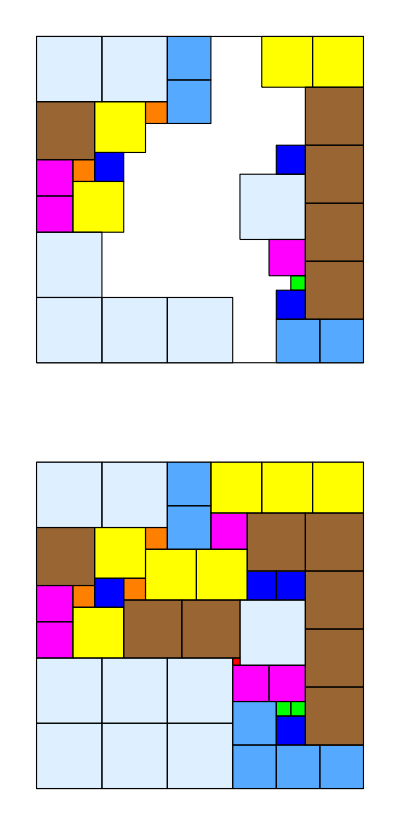

```mathematica
lst4= {
{kSky,0,0},{kSky,0,9},{kSky,36,0},{kSky,36,9},{kSky,36,18},
{kSky,27,0},{kCyan,0,18},{kCyan,6,18},{kOrange,9,15},
{kYellow,9,8},{kBrown,9,0},{kMagenta,17,0},{kMagenta,22,0},{kYellow,20,5},{kOrange,17,5},{kBlue,16,8},
{kYellow,0,31},{kYellow,0,38},
{kBrown,7,37},{kBrown,15,37},{kBrown,23,37},{kBrown,31,37},
{kCyan,39,39},{kCyan,39,33},{kBlue,35,33},{kGreen,33,35},
{kMagenta,28,32},{kSky,19,28},{kBlue,15,33}
}//Echo[#,Length,Length]&;
sols4="[(27, 27), (33, 35), (33, 33), (9, 15), (17, 5), (16, 12), (16, 8), (35, 33), (15, 33), (15, 29), (17, 0), (22, 0), (28, 32), (7, 24), (28, 27), (0, 18), (6, 18), (39, 39), (39, 33), (33, 27), (39, 27), (9, 8), (20, 5), (0, 31), (0, 38), (0, 24), (12, 15), (12, 22), (9, 0), (7, 37), (15, 37), (23, 37), (31, 37), (7, 29), (19, 12), (19, 20), (0, 0), (0, 9), (36, 0), (36, 9), (36, 18), (27, 0), (19, 28), (27, 9), (27, 18)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst4]},Map[PlotPartridgeTiling[9,#]&,sols4]}]
```

Length  24

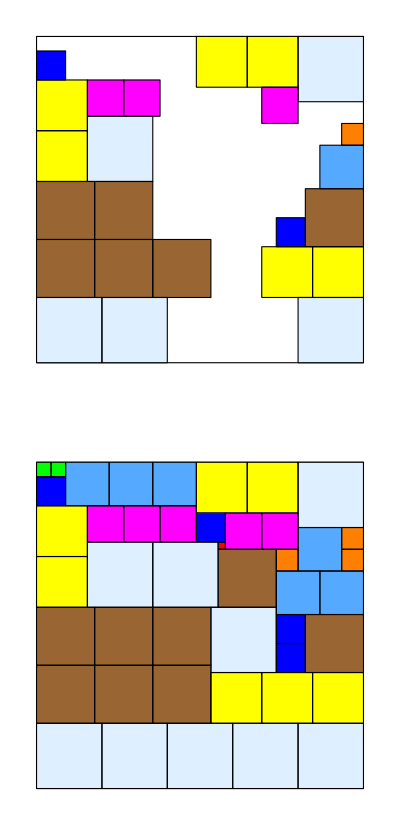

```mathematica
lst5= {
{kSky,36,0},{kSky,36,9},
{kBrown,28,0},{kBrown,28,8},{kBrown,28,16},{kBrown,20,0},{kBrown,20,8},{kYellow,13,0},{kYellow,6,0},
{kSky,11,7},{kMagenta,6,7},{kMagenta,6,12},{kBlue,2,0},
{kSky,36,36},{kYellow,29,31},{kYellow,29,38},{kBrown,21,37},
{kBlue,25,33},{kCyan,15,39},{kOrange,12,42},
{kSky,0,36},{kYellow,0,29},{kYellow,0,22},{kMagenta,7,31}
}//Echo[#,Length,Length]&;
sols5="[(11, 25), (0, 0), (0, 2), (12, 42), (9, 42), (12, 33), (2, 0), (25, 33), (7, 22), (21, 33), (6, 7), (6, 12), (7, 31), (6, 17), (7, 26), (15, 39), (0, 4), (0, 10), (0, 16), (9, 36), (15, 33), (13, 0), (6, 0), (29, 31), (29, 38), (0, 29), (0, 22), (29, 24), (28, 0), (28, 8), (28, 16), (20, 0), (20, 8), (21, 37), (12, 25), (20, 16), (36, 0), (36, 9), (11, 7), (36, 36), (0, 36), (11, 16), (20, 24), (36, 18), (36, 27)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst5]},Map[PlotPartridgeTiling[9,#]&,sols5]}]
```

Length  27

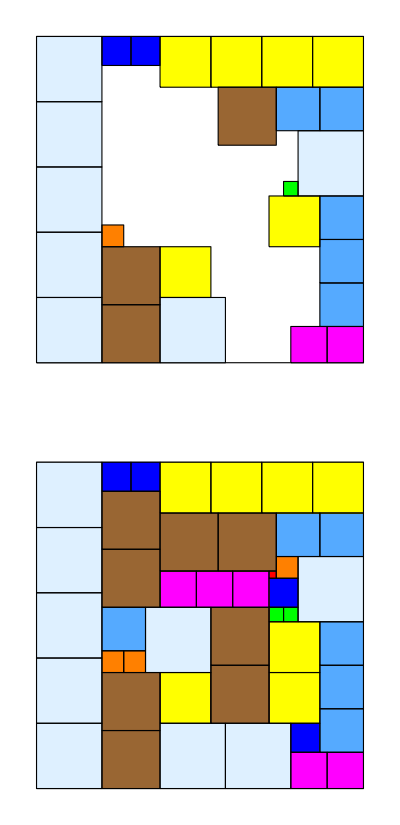

```mathematica
lst6= {
{kSky,0,0},{kSky,9,0},{kSky,18,0},{kSky,27,0},{kSky,36,0},
{kYellow,0,17},{kYellow,0,24},{kYellow,0,31},{kYellow,0,38},
{kBlue,0,9},{kBlue,0,13},{kCyan,7,33},{kCyan,7,39},{kBrown,7,25},
{kSky,13,36},{kGreen,20,34},{kCyan,22,39},{kCyan,28,39},{kCyan,34,39},{kMagenta,40,35},{kMagenta,40,40},{kYellow,22,32},
{kBrown,37,9},{kBrown,29,9},{kOrange,26,9},{kSky,36,17},{kYellow,29,17}
}//Echo[#,Length,Length]&;
sols6="[(15, 32), (20, 34), (20, 32), (26, 9), (13, 33), (26, 12), (0, 9), (0, 13), (16, 32), (36, 35), (40, 35), (40, 40), (15, 17), (15, 22), (15, 27), (7, 33), (7, 39), (22, 39), (28, 39), (34, 39), (20, 9), (0, 17), (0, 24), (0, 31), (0, 38), (22, 32), (29, 17), (29, 32), (7, 25), (37, 9), (29, 9), (4, 9), (7, 17), (12, 9), (20, 24), (28, 24), (0, 0), (9, 0), (18, 0), (27, 0), (36, 0), (13, 36), (36, 17), (20, 15), (36, 26)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst6]},Map[PlotPartridgeTiling[9,#]&,sols6]}]
```

Length  26

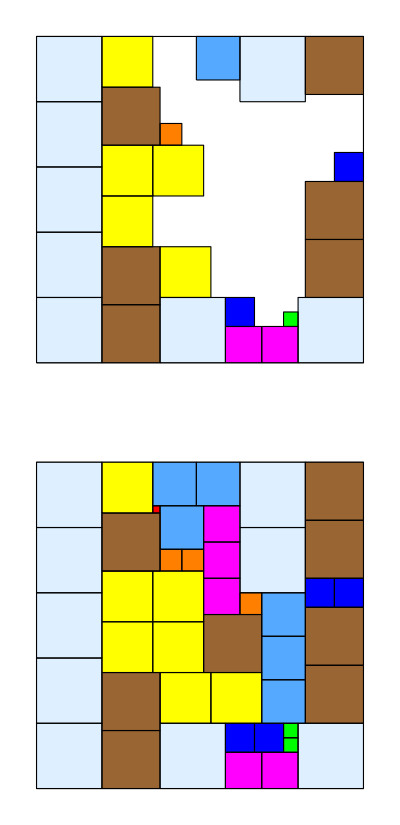

```mathematica
lst7= {
{kSky,0,0},{kSky,9,0},{kSky,18,0},{kSky,27,0},{kSky,36,0},
{kBrown,7,9},{kYellow,15,9},{kYellow,22,9},{kBrown,37,9},{kBrown,29,9},{kYellow,0,9},{kYellow,15,16},{kOrange,12,17},
{kSky,36,17},{kYellow,29,17},{kMagenta,40,26},{kMagenta,40,31},
{kBlue,36,26},{kGreen,38,34},{kSky,36,36},
{kBrown,28,37},{kBrown,20,37},{kBlue,16,41},
{kBrown,0,37},{kSky,0,28},{kCyan,0,22}
}//Echo[#,Length,Length]&;
sols7="[(6, 16), (38, 34), (36, 34), (12, 17), (12, 20), (18, 28), (36, 26), (16, 41), (16, 37), (36, 30), (40, 26), (40, 31), (6, 23), (11, 23), (16, 23), (0, 22), (0, 16), (6, 17), (18, 31), (24, 31), (30, 31), (15, 9), (22, 9), (0, 9), (15, 16), (29, 17), (22, 16), (29, 24), (7, 9), (37, 9), (29, 9), (28, 37), (20, 37), (0, 37), (8, 37), (21, 23), (0, 0), (9, 0), (18, 0), (27, 0), (36, 0), (36, 17), (36, 36), (0, 28), (9, 28)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst7]},Map[PlotPartridgeTiling[9,#]&,sols7]}]
```

Length  24

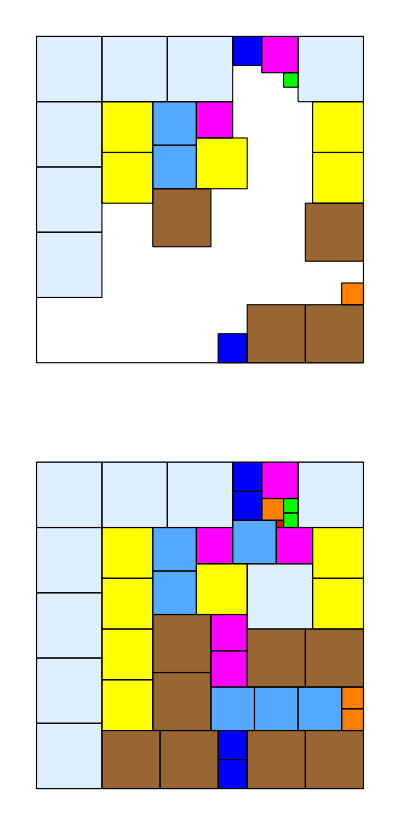

```mathematica
lst8= {
{kSky,0,0},{kSky,0,9},{kSky,0,18},{kSky,9,0},{kSky,18,0},{kSky,0,36},{kSky,27,0},
{kBlue,0,27},{kMagenta,0,31},{kGreen,5,34},{kYellow,9,38},{kYellow,16,38},{kBrown,23,37},
{kYellow,9,9},{kYellow,16,9},{kCyan,9,16},{kCyan,15,16},{kBrown,21,16},{kMagenta,9,22},{kYellow,14,22},
{kBrown,37,37},{kBrown,37,29},{kBlue,41,25},{kOrange,34,42}
}//Echo[#,Length,Length]&;
sols8="[(8, 33), (5, 34), (7, 34), (34, 42), (5, 31), (31, 42), (0, 27), (41, 25), (4, 27), (37, 25), (0, 31), (9, 22), (9, 33), (21, 24), (26, 24), (9, 16), (15, 16), (8, 27), (31, 24), (31, 30), (31, 36), (9, 38), (16, 38), (9, 9), (16, 9), (14, 22), (23, 9), (30, 9), (23, 37), (21, 16), (37, 37), (37, 29), (23, 29), (29, 16), (37, 9), (37, 17), (0, 0), (0, 9), (0, 18), (9, 0), (18, 0), (0, 36), (27, 0), (14, 29), (36, 0)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst8]},Map[PlotPartridgeTiling[9,#]&,sols8]}]
```

Length  25

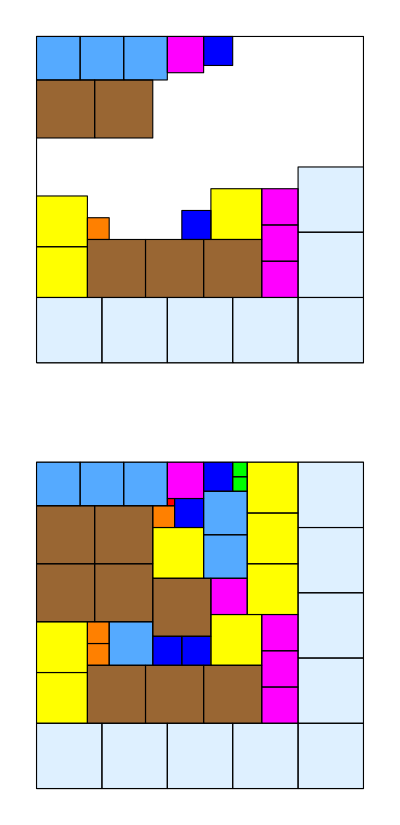

```mathematica
lst9= {
{kSky,36,0},{kSky,36,9},{kSky,36,18},{kSky,36,27},{kSky,36,36},
{kSky,27,36},{kSky,18,36},{kYellow,22,0},{kYellow,29,0},
{kBrown,28,7},{kBrown,28,15},{kBrown,28,23},
{kMagenta,31,31},{kMagenta,26,31},{kMagenta,21,31},
{kYellow,21,24},{kBlue,24,20},{kOrange,25,7},
{kCyan,0,0},{kCyan,0,6},{kCyan,0,12},{kMagenta,0,18},{kBlue,0,23},
{kBrown,6,0},{kBrown,6,8}
}//Echo[#,Length,Length]&;
sols9="[(5, 18), (0, 27), (2, 27), (25, 7), (6, 16), (22, 7), (24, 20), (0, 23), (5, 19), (24, 16), (31, 31), (26, 31), (21, 31), (0, 18), (16, 24), (0, 0), (0, 6), (0, 12), (4, 23), (10, 23), (22, 10), (22, 0), (29, 0), (21, 24), (0, 29), (7, 29), (9, 16), (14, 29), (28, 7), (28, 15), (28, 23), (6, 0), (6, 8), (14, 0), (14, 8), (16, 16), (36, 0), (36, 9), (36, 18), (36, 27), (36, 36), (27, 36), (18, 36), (0, 36), (9, 36)]"//ParseListPos[9];
GraphicsGrid[{{PlotPartridgeTiling[9,lst9]},Map[PlotPartridgeTiling[9,#]&,sols9]}]
```

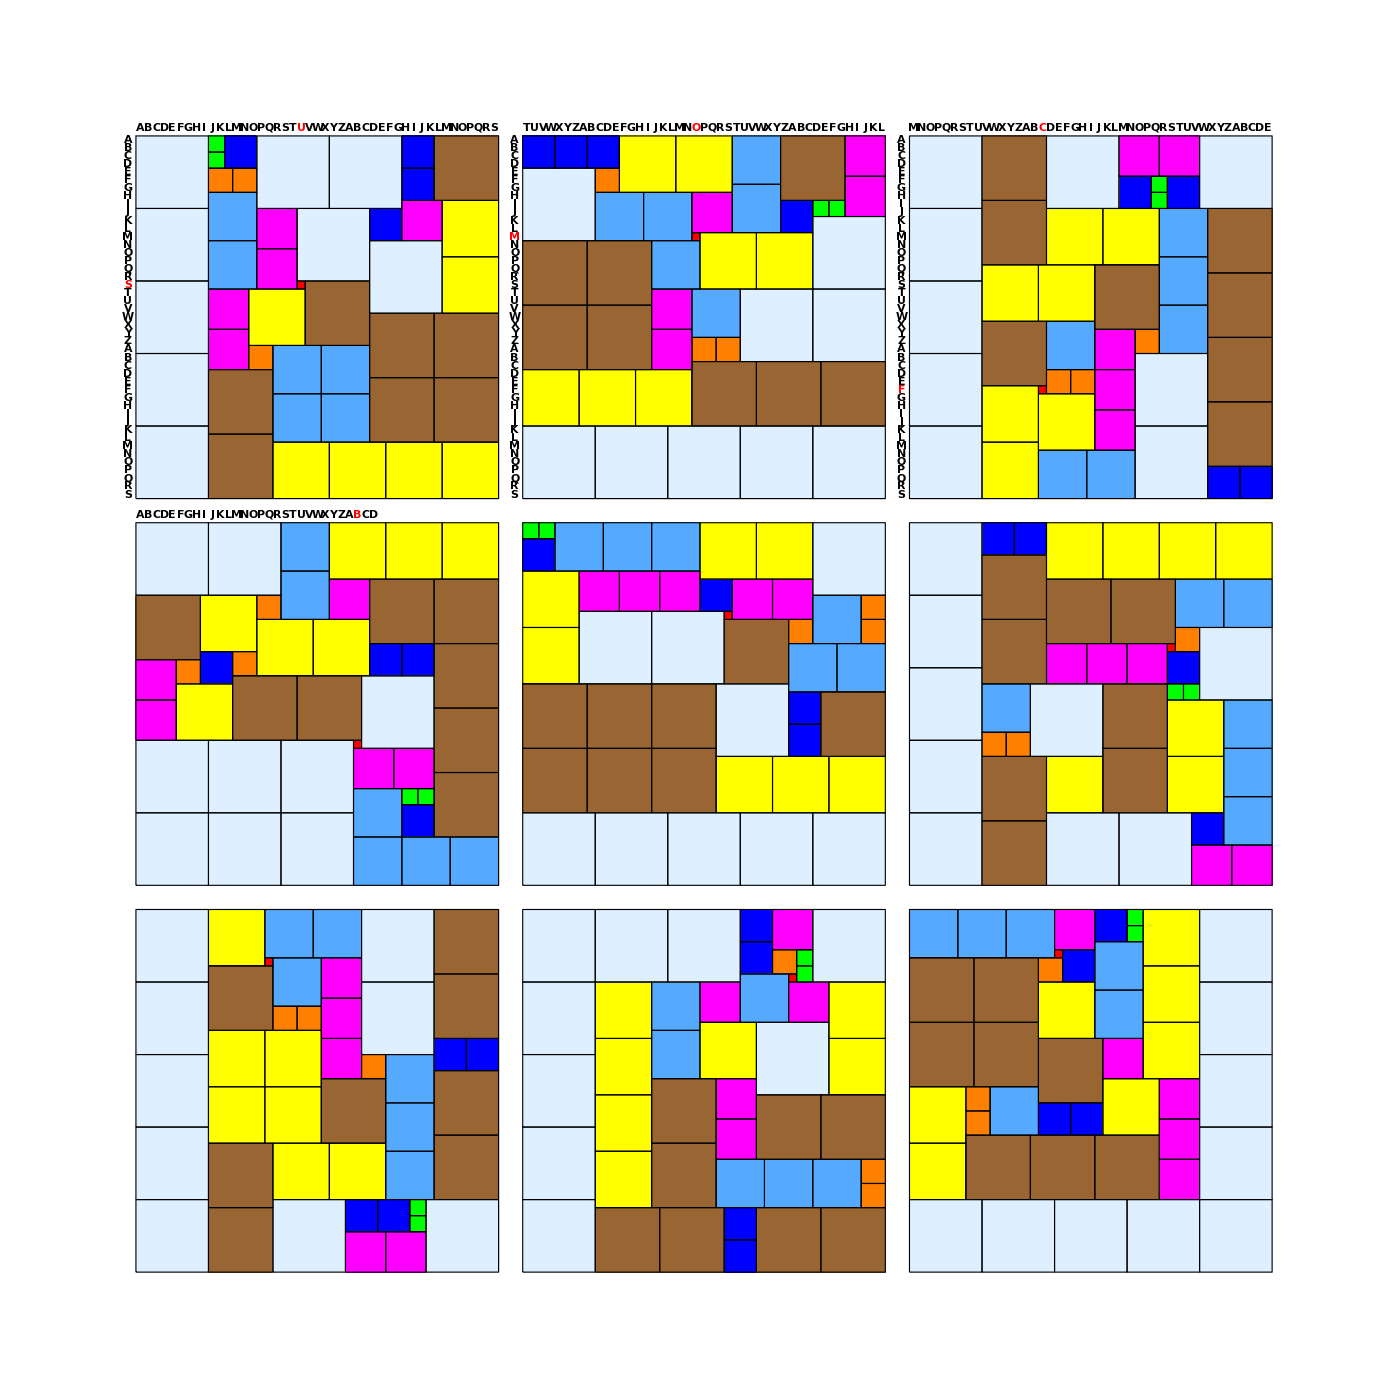

```mathematica
solgrid=Map[First,{{sols1,sols2,sols3},{sols4,sols5,sols6},{sols7,sols8,sols9}},{2}];
Graphics[Table[First[
PlotPartridgeTiling[9,DeleteCases[solgrid[[i,j]],{0,__}],
"ColumnLetters"->RepeatedAlphabet[9, j,{1+solgrid[[i, j,1,3]]}],
"RowLetters"->RepeatedAlphabet[9, i,{1+solgrid[[i, j,1,2]]}]]]/.
r:(_Rectangle|_Text):>GeometricTransformation[r,{IdentityMatrix[2],48{j-1,1-i}}],{i,3},{j,3}],ImageSize->1400,PlotRangePadding->0.1]
```

```mathematica
Flatten[Table[{Keys[RepeatedAlphabet[9, i]][[1+solgrid[[i,j,1,2]]]],Keys[RepeatedAlphabet[9,j]][[1+solgrid[[i,j,1,3]]]]},{i,3},{j,3}],1]
```

{{S,U},{M,O},{F,C},{U,B},{E,S},{I,S},{S,Q},{U,A},{R,E}}